## Practical 1 - Bisection Method

```mathematica
Bisection[a0_,b0_,k_]:=
Module[{},
a=N[a0];
b=N[b0];
m=(a+b)/2;
i=0;
output={{i,a,b,m,f[a],f[b],f[m],Sign[f[a]*f[m]]}};
While[i<k,If[Sign[f[b]]*Sign[f[m]]<0,a=m,b=m;];
m=(a+b)/2;
i=i+1;
output=Append[output,{i,a,b,m,f[a],f[b],f[m],Sign[f[a]*f[m]]}];];
Print[
NumberForm[
TableForm[output,
TableHeadings-> {None,{"i","a0","a1","a2","f[a0]","f[a1]","f[a2]","Sign[f[a0]*f[a2]]"}}],16]];
Print["m= ",NumberForm[m,16]];]
```

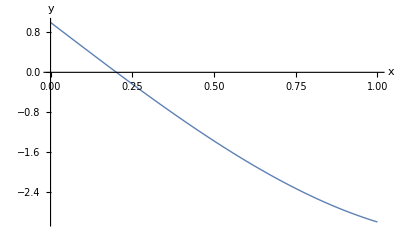

y=f[x]= 1-5 x+x^3

i | a0 | a1 | a2 | f[a0] | f[a1] | f[a2] | Sign[f[a0]*f[a2]]
0 | 0. | 1. | 0.5 | 1. | -3. | -1.375 | -1
1 | 0. | 0.5 | 0.25 | 1. | -1.375 | -0.234375 | -1
2 | 0. | 0.25 | 0.125 | 1. | -0.234375 | 0.376953125 | 1
3 | 0.125 | 0.25 | 0.1875 | 0.376953125 | -0.234375 | 0.069091796875 | 1
4 | 0.1875 | 0.25 | 0.21875 | 0.069091796875 | -0.234375 | -0.083282470703125 | -1
5 | 0.1875 | 0.21875 | 0.203125 | 0.069091796875 | -0.083282470703125 | -0.007244110107421875 | -1

m= 0.203125

```mathematica
f[x_]:=x^3-5*x+1
Plot[f[x],{x,0,1},PlotStyle-> {Thick},AxesLabel-> {x,y}]
Print["y=f[x]= ",f[x]];
Bisection[0,1,5]
```

## Practical 2 - Newton Raphson

```mathematica
NewtonRaphson[x0_,n_,f_]:=Module[{xk1,xk=N[x0]},k=0;
Output={{k,x0,f[x0]}};
While[k<n,fPrimexk=f'[xk];If[fPrimexk==0,Print["The Derivative of function at ",k,"th iteration is zero, we cannot proceed further with the iterative scheme"];
Break[]];
xk1=xk-f[xk]/fPrimexk;
xk=xk1;
k++;
Output=Append[Output,{k,xk,f[xk]}];];
Print[NumberForm[TableForm[Output,TableHeadings->{None,{"k","xk","f[xk]"}}],10]];
Print["Root After",n,"iterations xk=",NumberForm[xk,10]];
Print["Function value at approximated root, f[xk]=",NumberForm[f[xk],6]];];
```

```mathematica
f[x_]:=x^3-5*x+1
Plot[f[x],{x,0,1},PlotStyle->{Thick},AxesLabel->{x,y}]
Print["y=f[x]=",f[x]];
NewtonRaphson[0.5,5,f]
```

-Graphics-

y=f[x]=1-5 x+x^3

k | xk | f[xk]
0 | 0.5 | -1.375
1 | 0.1764705882 | 0.1231426827
2 | 0.2015680743 | 0.0003492763989
3 | 0.2016396751 | 3.100484314×10^-9
4 | 0.2016396757 | 1.110223025×10^-16
5 | 0.2016396757 | 1.110223025×10^-16

Root After5iterations xk=0.2016396757

Function value at approximated root, f[xk]=1.11022×10^-16

## Practical 3 - Secant Method

```mathematica
Secant[a0_,b0_,n_]:=
Module[{},
a=N[a0];
b=N[b0];
c=(a*f[b]-b*f[a])/(f[b]-f[a]);
i=0;
Output={{i,a,b,c,f[c]}};
While[i<n,a=b;b=c;
c=(a*f[b]-b*f[a])/(f[b]-f[a]);
i=i+1;
Output=Append[Output,{i,a,b,c,f[c]}];];
Print[
NumberForm[
TableForm[Output,TableHeadings-> {None,{"i","a","b","f[c]"}}],16]];
Print["c= ",NumberForm[c,16]];]
```

```mathematica
f[x_]:=x^3-5*x+1
Plot[f[x],{x,0,1},PlotStyle->{Thick},AxesLabel->{x,y}]
Print["y=f[x]= ",f[x]]
Secant[0,1,6]
```

-Graphics-

y=f[x]= 1-5 x+x^3

i | a | b | f[c] | 
0 | 0. | 1. | 0.25 | -0.234375
1 | 1. | 0.25 | 0.1864406779661017 | 0.07427731170178065
2 | 0.25 | 0.1864406779661017 | 0.2017362561791272 | -0.0004711161687362964
3 | 0.1864406779661017 | 0.2017362561791272 | 0.2016398528913041 | -8.64229303898512×10^-7
4 | 0.2017362561791272 | 0.2016398528913041 | 0.2016396757212823 | 1.035271868232712×10^-11
5 | 0.2016398528913041 | 0.2016396757212823 | 0.2016396757234047 | -2.220446049250313×10^-16
6 | 0.2016396757212823 | 0.2016396757234047 | 0.2016396757234046 | 1.110223024625157×10^-16

c= 0.2016396757234046

## Practical 4 - LU Decomposition

```mathematica
LUDecom[A0_,n_]:=
Module[{A=A0,i,p},U=A0;L=IdentityMatrix[n];
Print[MatrixForm[L],MatrixForm[U],"=",MatrixForm[A0]];
For[p=1,p≤ n-1,p++,
For[i=p+1,i≤ n,i++,
m=A_[[i,p]]/A_[[p,p]];
L_[[i,p]] = m;
A_[[i]] = A_[[i]] - m A_[[p]] ;
U=A;
Print[MatrixForm[L],MatrixForm[U],"=",MatrixForm[A0]];];];];
Print["L","=",MatrixForm[L]];
Print["U","=",MatrixForm[U]];
A=({{4, 2, 3}, {-3, 1, 4}, {2, 4, 5}});
LUDecom[A,3]
```

L=L

U=U

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)(4 | 2 | 3
-3 | 1 | 4
2 | 4 | 5)=(4 | 2 | 3
-3 | 1 | 4
2 | 4 | 5)

(1 | 0 | 0
-3/4 | 1 | 0
0 | 0 | 1)(4 | 2 | 3
0 | 5/2 | 25/4
2 | 4 | 5)=(4 | 2 | 3
-3 | 1 | 4
2 | 4 | 5)

(1 | 0 | 0
-3/4 | 1 | 0
1/2 | 0 | 1)(4 | 2 | 3
0 | 5/2 | 25/4
0 | 3 | 7/2)=(4 | 2 | 3
-3 | 1 | 4
2 | 4 | 5)

(1 | 0 | 0
-3/4 | 1 | 0
1/2 | 6/5 | 1)(4 | 2 | 3
0 | 5/2 | 25/4
0 | 0 | -4)=(4 | 2 | 3
-3 | 1 | 4
2 | 4 | 5)

## Practical 5 - Gauss Jacobi

```mathematica
Jacobi[A0_,B0_,X0_,max_]:=
Module[{A=N[A0],B=N[B0],i,j,k=0,n=Length[X0],X=X0,Xold=X0},
Print["X",0,"=",X];
While[k<max,For[i=1,i≤n,i=i+1,
X[[i]]=(B[[i]]+A[[i,i]]*Xold[[i]]-∑_(j=1)^n A[[i,j]]*Xold[[j]])/A[[i,i]]];
Print["X",k+1,"=",X];
Xold=X;
k=k+1;];];
```

```mathematica
A0={{4,1,0,1},{1,4,1,0},{0,1,4,1},{1,0,1,4}};
B0={2,-2,2,-2};
X0={0,0,0,0};
Jacobi[A0,B0,X0,10];
```

X0={0,0,0,0}

X1={0.5,-0.5,0.5,-0.5}

X2={0.75,-0.75,0.75,-0.75}

X3={0.875,-0.875,0.875,-0.875}

X4={0.9375,-0.9375,0.9375,-0.9375}

X5={0.96875,-0.96875,0.96875,-0.96875}

X6={0.984375,-0.984375,0.984375,-0.984375}

X7={0.992188,-0.992188,0.992188,-0.992188}

X8={0.996094,-0.996094,0.996094,-0.996094}

X9={0.998047,-0.998047,0.998047,-0.998047}

X10={0.999023,-0.999023,0.999023,-0.999023}

## Practical 6 - Gauss Seidel

```mathematica
Seidel[A0_,B0_,X0_,max_]:=
Module[{A=N[A0],B=N[B0],i,j,k=0,n=Length[X0],X=X0,Xold=X0},
Print["X",0,"=",X];
While[k<max,For[i=1,i≤n,i=i+1,
X[[i]]=(B[[i]]-∑_(j=1)^(i-1) A[[i,j]]*X[[j]]-∑_(j=i+1)^n A[[i,j]]*Xold[[j]])/A[[i,i]]];
Print["x",k+1,"=",NumberForm[X,10]];
Xold=X;
k=k+1;];];
```

```mathematica
A0={{2,-1,0,0},{-1,2,-1,0},{0,-1,2,-1},{0,0,-1,2}};
B0={1,0,0,1};
X0={0.5,0.5,0.5,0.5};
Seidel[A0,B0,X0,10]
```

X0={0.5,0.5,0.5,0.5}

x1={0.75,0.625,0.5625,0.78125}

x2={0.8125,0.6875,0.734375,0.8671875}

x3={0.84375,0.7890625,0.828125,0.9140625}

x4={0.89453125,0.861328125,0.8876953125,0.9438476563}

x5={0.9306640625,0.9091796875,0.9265136719,0.9632568359}

x6={0.9545898438,0.9405517578,0.9519042969,0.9759521484}

x7={0.9702758789,0.9610900879,0.9685211182,0.9842605591}

x8={0.9805450439,0.9745330811,0.9793968201,0.98969841}

x9={0.9872665405,0.9833316803,0.9865150452,0.9932575226}

x10={0.9916658401,0.9890904427,0.9911739826,0.9955869913}

## Practical 7 - Lagranges Interpolation

```mathematica
lagrange[x0_,f0_]:=
Module[{xi=x0,fi=f0,n,m,polynomial},
n=Length[xi];
m=Length[fi];
For[i=1,i≤ n,i=i+1,
L[i,x_]=( ∏_(j=1)^(i-1) (x-xi[[j]])/(xi[[i]]-xi[[j]]))
(∏_(j=i+1)^n (x-xi[[j]])/(xi[[i]]-xi[[j]]));];
polynomial[x]=∑_(k=1)^n L[k,x]*fi[[k]];
Return[polynomial[x]];]
```

```mathematica
nodes={0,1,3};
values={1,3,55};
lagrangepolynomial[x_]=lagrange[nodes,values]
lagrangepolynomial[x_]=Simplify[lagrangepolynomial[x]]
Print["Lagrange Polynomial= ",lagrangepolynomial[x]]
lagrangepolynomial[2]
```

lagrange[{0,1,3},{1,3,55}]

lagrange[{0,1,3},{1,3,55}]

Lagrange Polynomial= lagrange[{0,1,3},{1,3,55}]

lagrange[{0,1,3},{1,3,55}]

## Practical 8 - Newton interpolation

```mathematica
Question.Use the table given below to estimate the
value of f (1.5) through Newton' s Interpolation Polynomial
i 0 1 2 3
x 1 2 3 4
log (xi) 0 0.3010 0.4771 0.6021
```

```mathematica
sum=0;
points={{1,0},{2,0.3010},{3,0.4771},{4,0.6021}};
n=Length[points]
y=points⟦All,1⟧
f=points⟦All,2⟧
dd[k_]:=Sum[(f⟦i⟧/Product[If[Equal[j,i],1,(y⟦i⟧-y⟦j⟧)],{j,1,k}]),{i,1,k}]
p[x_]:=Sum[(dd[i]*Product[If[i≤j,1,x-y⟦j⟧],{j,1,i-1}]),{i,1,n}]
Simplify[p[x]]
Evaluate[p[1.5]]
```

4

{1,2,3,4}

{0,0.301,0.4771,0.6021}

-0.4997+0.62365 x-0.13625 x^2+0.0123 x^3

0.170725

## Practical 9 - Trapezoidal Rule

```mathematica
Quit[]
```

```mathematica
Trap[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],k,n=n0,X},h=(b-a)/n;
Subscript[X, k_]=a+k*h;
Return[h/2(f[a]+f[b])+h∑_(k=1)^(n-1) f[Subscript[X, k]]];]
f[x_]:=1/(1+x);
Print["The value of ∫_0^1 1/(1 + x)ⅆx, using TR is: ",N[Trap[0,1,10]]]
```

The value of ∫_0^1 1/(1 + x)ⅆx, using TR is: 0.693771

## Practical 10 - Simpsons Rule

```mathematica
Simp[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],k,n=n0,X},h=(b-a)/(2*n);
Subscript[X, k_]=a+k*h;
Return[h/3(f[a]+f[b])+(2h)/3∑_(k=1)^(n-1) f[Subscript[X, 2k]]+(4h)/3*∑_(k=1)^n f[Subscript[X, 2k-1]]];]
f[x_]:=1/(1+x);
Print["The value of ∫_0^1 1/(1 + x)ⅆx, using Simpsons Rule is: ",N[Simp[0,1,2]]]
```

The value of ∫_0^1 1/(1 + x)ⅆx, using Simpsons Rule is: 0.693254

## Practical 11 - Eulers Method

```mathematica
Euler[{t_,y_}]:={t+h,y+h*f[t,y]}
f[t_,y_]:=1+(y/t)
h=0.5
points=NestList[Euler,{1,1},10]
TableForm[points,TableHeadings->{Automatic,{"t_i","y_i"}}]
```

0.5

{{1,1},{1.5,2.},{2.,3.16667},{2.5,4.45833},{3.,5.85},{3.5,7.325},{4.,8.87143},{4.5,10.4804},{5.,12.1448},{5.5,13.8593},{6.,15.6193}}

| t_i | y_i
1 | 1 | 1
2 | 1.5 | 2.
3 | 2. | 3.16667
4 | 2.5 | 4.45833
5 | 3. | 5.85
6 | 3.5 | 7.325
7 | 4. | 8.87143
8 | 4.5 | 10.4804
9 | 5. | 12.1448
10 | 5.5 | 13.8593
11 | 6. | 15.6193

## Practical 12 - RK Method

```mathematica
Quit[]
RK4[a0_,b0_,α_,m0_]:=
Module{a=a0,b=b0,j,m=m0},h=(b-a)/m;
Y=T=Table[0,{m+1}];
T⟦1⟧=a;
Y⟦1⟧=α;
Forj=1,j≤m,j++,
K1=h f[T⟦j⟧,Y⟦j⟧];
K2=h fT⟦j⟧+h/2,Y⟦j⟧+K1/2 ;
K3=h fT⟦j⟧+h/2,Y⟦j⟧+K2/2;
K4=h*f[T⟦j⟧+h,Y⟦j⟧+K3];
Y⟦j+1⟧=Y⟦j⟧+1/6(K1+2*K2+2*K3+K4);
T⟦j+1⟧=a+h j;;
Return[Transpose[{T,Y}]]
f[t_,y_]:=1+y/t;
points=RK4[1,5,1,8];
TableForm[points,TableHeadings->{Automatic,{"ti","yi3"}}]
```

Syntax::tsntxi: "RK4[a0_,b0_,α_,m0_]:=Module{a=a0,b=b0,j,m=m0},h=(b-a)/m;" is incomplete; more input is needed.